# Nonlinear EVC test

### Initializing global parameters:

```mathematica
Xmin=-10;                                    (* Lower limit range for the function *)
Xmax=10;                                      (* Upper limit range for the function *)
dx=0.5;                                       (*Step size for the finite element method*)
x=Range[Xmin,Xmax,dx]; (*Initialize the abcissa*)
len=Length[x];     (*Initialize the lengeth of solution vector*)

(*Laplacian matrix for the discrete system*)
lap=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{len,len}]/dx^2;
```

### Variable initialization:

#### Placeholders for solving the differential equation `exactly’

```mathematica
phi1=Array[phiVal1,len];(* Placeholder for a particular eigenfunction we are calculating *)
psi1=Array[phiVal1,len];(* Placeholder for a particular dual function we are calculating *)
phi2=Array[phiVal2,len];(* Placeholder for a particular eigenfunction we are calculating *)
psi2=Array[phiVal2,len];(* Placeholder for a particular dual function we are calculating *)
lam;(* Placeholder for a particular eigenvalue we are calculating *)
```

### Eigenvalue Problem definition:

We are interested in solving for the stationary states of the Gross-Pitaevskii equation in 1 dimension with a harmonic potential:
fig = plt.figure()
ax = plt.axes()

isospin = 0
i_s = 0
i_l = 0
i_n = 1

x = np.linspace(0, 20, 2001)
ax.plot(x[:1000],trial_wf[isospin,i_s,i_l,i_n,:1000],color=’black’)
for i in range(len(train_wfs)):
    ax.plot(x[:1000],train_wfs[i][isospin,i_s,i_l,i_n,:1000],linestyle=”:”)
#ax.plot(trial_wf[isospin,i_s,i_l,i_n,:],linestyle=’--‘)

```mathematica
q0=200; (*Nonlinear coupling for the Gross–Pitaevskii equation*)
k0=1;      (*Coupling constant for the harmonic potential*)

eigEq1[q_,k_]:=(Dot[-lap,phi1]+k*(x^2)*phi1+q*(phi1^2+phi2^2)*phi1==lam1*phi1);(*Eigenvalue equation*)
eigEq2[q_,k_]:=(Dot[-lap,phi2]+(k+1)*(x^2)*phi2+q*(phi1^2+phi2^2)*phi2==lam2*phi2);(*Eigenvalue equation*)
normEq1[q_,k_]:=Dot[phi1,phi1]==1;(*Normalization condition*)
normEq2[q_,k_]:=Dot[phi2,phi2]==1;(*Normalization condition*)

eqns[q_,k_]:=Join[Thread[eigEq1[q,k]],Thread[eigEq2[q,k]],{normEq1[q,k],normEq2[q,k]}]; (*Full (n+1) equation set*)
```

### Example for finding the lowest energy solution:

We utilize FindRoot to find the solution to the eigenvalue equation. We use an eigenfunction of the harmonic oscillator, or a constant function, as an initial guess to speed up calculations. FindRoot allows us to bypass finding all of the other eigenfunctions we don’t care about by starting near the basin of attraction of the first eigenmode.

```mathematica
guess1=Exp[0*x]; (*Harmonic oscillator eigenfunction guess| NOT Really, a bunch of "1" as a guess*)
guess2=Exp[0*x]; (*Harmonic oscillator eigenfunction guess*)
sol2=FindRoot[eqns[200,k0],Join[Transpose[{Prepend[phi1,lam1],Prepend[guess1,1]}],Transpose[{Prepend[phi2,lam2],Prepend[guess2,1]}]],PrecisionGoal->20]; (*Solution routine for the full set of (n+1) equations*)
```

```mathematica
lam/.sol2 (*Sanity check station: We can check lambda for q=0 to verify we get the harmonic oscillator eigenvalue*)
```

lam

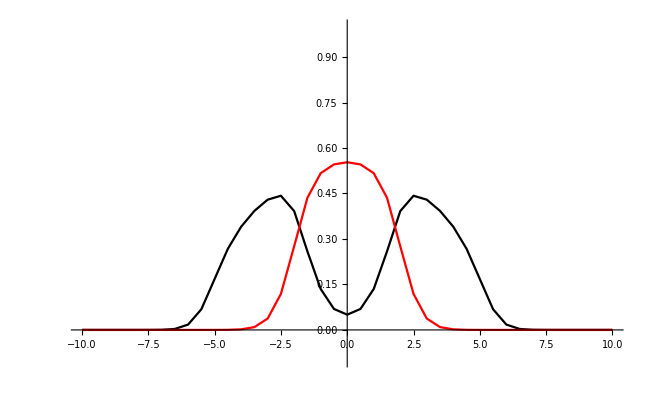

```mathematica
Show[ListPlot[Transpose[{x,Flatten[phi1/.sol2]/Sqrt[dx]}],PlotRange->{{-10,10},{-.1,1}},PlotStyle->{Black},Joined->True],ListPlot[Transpose[{x,Flatten[phi2/.sol2]/Sqrt[dx]}],PlotRange->{{-10,10},{-.1,1}},PlotStyle->{Red},Joined->True]]
```

### Manipulate to observe the solutions

```mathematica
{phi1,phi2}/.sol2
```

{{4.58175×10^-11,9.18402×10^-10,1.61248×10^-8,2.45707×10^-7,3.20443×10^-6,0.0000351466,0.000316886,0.00227647,0.0124486,0.0481721,0.11874,0.189279,0.240631,0.277559,0.303772,0.312926,0.277126,0.183046,0.0954922,0.0489492,0.035549,0.0489492,0.0954922,0.183046,0.277126,0.312926,0.303772,0.277559,0.240631,0.189279,0.11874,0.0481721,0.0124486,0.00227647,0.000316886,0.0000351466,3.20443×10^-6,2.45707×10^-7,1.61248×10^-8,9.18402×10^-10,4.58175×10^-11},{8.28675×10^-19,3.66814×10^-17,1.44405×10^-15,5.0166×10^-14,1.52311×10^-12,3.99544×10^-11,8.9306×10^-10,1.67184×10^-8,2.5641×10^-7,3.13016×10^-6,0.0000294993,0.000217231,0.0013133,0.00655988,0.0265282,0.0840112,0.19519,0.30832,0.365478,0.386005,0.391048,0.386005,0.365478,0.30832,0.19519,0.0840112,0.0265282,0.00655988,0.0013133,0.000217231,0.0000294993,3.13016×10^-6,2.5641×10^-7,1.67184×10^-8,8.9306×10^-10,3.99544×10^-11,1.52311×10^-12,5.0166×10^-14,1.44405×10^-15,3.66814×10^-17,8.28675×10^-19}}

```mathematica
sol[q_,k_]:=FindRoot[eqns[q,k],Join[Transpose[{Prepend[phi1,lam1],Prepend[guess1,1]}],Transpose[{Prepend[phi2,lam2],Prepend[guess2,1]}]],PrecisionGoal->20];(*Solution routine for the full set of (n+1) equations, as a function of a and/or k*)
```

```mathematica
Manipulate[Show[ListPlot[Transpose[{x,Flatten[phi1/.sol[q,k]]/Sqrt[dx]}],PlotRange->{{-10,10},{-.1,1}},PlotStyle->{Black},Joined->True],ListPlot[Transpose[{x,Flatten[phi2/.sol[q,k]]/Sqrt[dx]}],PlotRange->{{-10,10},{-.1,1}},PlotStyle->{Red},Joined->True]]
,{q,0,200},{k,0.1,10}] (*NOTE: The root algorithm does not always converge to the smallest eigenfunction for large or negative a, I need a fast method to find the eigenpair that reliable converges to the first root*)
```

## Galerkin Method with EVC:

### Initialization of the Galerkin Method vectors

```mathematica
K0=1;(*Fixed value of k for now*)
```

```mathematica
listQ=Range[0.0,200,50]; (*Training alpha values*)
numTrain=Length[listQ]; (*Number of training points*)
```

```mathematica
listPhi1=Array[trainPhi1,{numTrain,len}]; (*List of the training functions 'phi'*)
listPhi2=Array[trainPhi2,{numTrain,len}];(*List of the training functions 'phi'*)
```

```mathematica
listPsi1=Array[trainPsi1,{numTrain,len}];(*List of the training dual functions 'psi'*)
listPsi2=Array[trainPsi2,{numTrain,len}];(*List of the training dual functions 'psi'*)
listCoeff1=Array[aTest1,numTrain];
listCoeff2=Array[aTest2,numTrain];(*Coefficients of the Galerkin approximated solution*)
```

### Populate the arrays by solving the differential equation

```mathematica
For[i=1,i<=numTrain,i++,
{listPhi1[[i]],listPhi2[[i]]}={phi1,phi2}/.sol[listQ[[i]],K0];
{listPsi1[[i]],listPsi2[[i]]}={listPhi1[[i]],listPhi2[[i]]} ; (*psi=phi for the first flavor of the galerkin method*)
]
{listPhi1[[1]],listPhi2[[1]]}
```

{{3.2809×10^-18,8.77772×10^-17,2.13115×10^-15,4.6806×10^-14,9.25399×10^-13,1.63827×10^-11,2.58191×10^-10,3.59932×10^-9,4.40727×10^-8,4.70357×10^-7,4.33799×10^-6,0.0000342508,0.000229132,0.00128417,0.00595602,0.0225635,0.0688753,0.167117,0.318246,0.470639,0.536656,0.470639,0.318246,0.167117,0.0688753,0.0225635,0.00595602,0.00128417,0.000229132,0.0000342508,4.33799×10^-6,4.70357×10^-7,4.40727×10^-8,3.59932×10^-9,2.58191×10^-10,1.63827×10^-11,9.25399×10^-13,4.6806×10^-14,2.13115×10^-15,8.77772×10^-17,3.2809×10^-18},{1.28574×10^-22,6.64144×10^-21,3.10554×10^-19,1.30846×10^-17,4.94018×10^-16,1.66128×10^-14,4.94227×10^-13,1.29096×10^-11,2.9358×10^-10,5.75723×10^-9,9.63096×10^-8,1.35745×10^-6,0.0000158937,0.000152088,0.00116726,0.00703177,0.0324407,0.111521,0.277526,0.486392,0.587983,0.486392,0.277526,0.111521,0.0324407,0.00703177,0.00116726,0.000152088,0.0000158937,1.35745×10^-6,9.63096×10^-8,5.75723×10^-9,2.9358×10^-10,1.29096×10^-11,4.94227×10^-13,1.66128×10^-14,4.94018×10^-16,1.30846×10^-17,3.10554×10^-19,6.64144×10^-21,1.28574×10^-22}}

```mathematica
phi1
```

{phiVal1[1],phiVal1[2],phiVal1[3],phiVal1[4],phiVal1[5],phiVal1[6],phiVal1[7],phiVal1[8],phiVal1[9],phiVal1[10],phiVal1[11],phiVal1[12],phiVal1[13],phiVal1[14],phiVal1[15],phiVal1[16],phiVal1[17],phiVal1[18],phiVal1[19],phiVal1[20],phiVal1[21],phiVal1[22],phiVal1[23],phiVal1[24],phiVal1[25],phiVal1[26],phiVal1[27],phiVal1[28],phiVal1[29],phiVal1[30],phiVal1[31],phiVal1[32],phiVal1[33],phiVal1[34],phiVal1[35],phiVal1[36],phiVal1[37],phiVal1[38],phiVal1[39],phiVal1[40],phiVal1[41]}

### Define the Galerkin equations

```mathematica
qTest=175; (*Test Value of a, for sanity checks and to test the resuls of our scheme*)
```

```mathematica
testPhi1=Dot[Transpose[listPhi1],listCoeff1];(*Definition for the test function Phi*)
testPhi2=Dot[Transpose[listPhi2],listCoeff2]; (*Definition for the test function Phi*)
```

```mathematica
(*Error in the listPsi2[[1]] WATCH OUT WITH THIS ONE*)
```

```mathematica
eigGaler={};

For[ij=1,ij≤numTrain,ij++,
AppendTo[eigGaler,
(Dot[listPsi1[[ij]],
Dot[-lap,testPhi1]+K0*(x^2)*testPhi1+qTest*testPhi1*(testPhi1^2+testPhi2^2)]-Dot[listPsi1[[ij]],lam21*testPhi1])==0];

AppendTo[eigGaler,(Dot[listPsi2[[ij]],
Dot[-lap,testPhi2]+(K0+1)*(x^2)*testPhi2+qTest*testPhi2*(testPhi1^2+testPhi2^2)]-Dot[listPsi2[[ij]],lam22*testPhi2])==0];


]
```

```mathematica
(*NOTE: transform this into an Automatic equation*)
(*NOTE: the Simplify[] step is necessary, I don't know why. It is also REALLY SLOW*)
normGaler={Dot[testPhi1,testPhi1]==1,Dot[testPhi2,testPhi2]==1};

eqnsGaler=Join[eigGaler,normGaler];(*Full equation set*)
```

### Solve the equations for a test value

```mathematica
solGaler=FindRoot[eqnsGaler,Transpose[{Join[{lam21,lam22},listCoeff1,listCoeff2],Join[{5,8},ConstantArray[0.1,numTrain],ConstantArray[0.1,numTrain]]}],PrecisionGoal->20];
```

```mathematica
sol[qTest,1]
```

{lam1→25.4781,phiVal1[1]→1.5523×10^-11,phiVal1[2]→3.20247×10^-10,phiVal1[3]→5.81072×10^-9,phiVal1[4]→9.19567×10^-8,phiVal1[5]→1.25335×10^-6,phiVal1[6]→0.0000144851,phiVal1[7]→0.00013915,phiVal1[8]→0.00108209,phiVal1[9]→0.00656224,phiVal1[10]→0.0293166,phiVal1[11]→0.0881473,phiVal1[12]→0.166407,phiVal1[13]→0.228769,phiVal1[14]→0.272874,phiVal1[15]→0.303889,phiVal1[16]→0.318106,phiVal1[17]→0.291224,phiVal1[18]→0.20345,phiVal1[19]→0.111823,phiVal1[20]→0.0599726,phiVal1[21]→0.0446193,phiVal1[22]→0.0599726,phiVal1[23]→0.111823,phiVal1[24]→0.20345,phiVal1[25]→0.291224,phiVal1[26]→0.318106,phiVal1[27]→0.303889,phiVal1[28]→0.272874,phiVal1[29]→0.228769,phiVal1[30]→0.166407,phiVal1[31]→0.0881473,phiVal1[32]→0.0293166,phiVal1[33]→0.00656224,phiVal1[34]→0.00108209,phiVal1[35]→0.00013915,phiVal1[36]→0.0000144851,phiVal1[37]→1.25335×10^-6,phiVal1[38]→9.19567×10^-8,phiVal1[39]→5.81072×10^-9,phiVal1[40]→3.20247×10^-10,phiVal1[41]→1.5523×10^-11,lam2→28.3537,phiVal2[1]→5.00039×10^-19,phiVal2[2]→2.24575×10^-17,phiVal2[3]→8.98623×10^-16,phiVal2[4]→3.17992×10^-14,phiVal2[5]→9.8604×10^-13,phiVal2[6]→2.65041×10^-11,phiVal2[7]→6.09577×10^-10,phiVal2[8]→1.18064×10^-8,phiVal2[9]→1.88725×10^-7,phiVal2[10]→2.42528×10^-6,phiVal2[11]→0.000024244,phiVal2[12]→0.000185502,phiVal2[13]→0.00113479,phiVal2[14]→0.00571686,phiVal2[15]→0.0234227,phiVal2[16]→0.0756964,phiVal2[17]→0.182048,phiVal2[18]→0.301508,phiVal2[19]→0.368104,phiVal2[20]→0.393032,phiVal2[21]→0.39916,phiVal2[22]→0.393032,phiVal2[23]→0.368104,phiVal2[24]→0.301508,phiVal2[25]→0.182048,phiVal2[26]→0.0756964,phiVal2[27]→0.0234227,phiVal2[28]→0.00571686,phiVal2[29]→0.00113479,phiVal2[30]→0.000185502,phiVal2[31]→0.000024244,phiVal2[32]→2.42528×10^-6,phiVal2[33]→1.88725×10^-7,phiVal2[34]→1.18064×10^-8,phiVal2[35]→6.09577×10^-10,phiVal2[36]→2.65041×10^-11,phiVal2[37]→9.8604×10^-13,phiVal2[38]→3.17992×10^-14,phiVal2[39]→8.98623×10^-16,phiVal2[40]→2.24575×10^-17,phiVal2[41]→5.00039×10^-19}

```mathematica
solGaler
```

{lam21→25.4761,lam22→28.3562,aTest1[1]→-0.00203909,aTest1[2]→0.0200421,aTest1[3]→-0.125732,aTest1[4]→0.682049,aTest1[5]→0.426087,aTest2[1]→-0.000537716,aTest2[2]→0.0312835,aTest2[3]→-0.19149,aTest2[4]→0.791265,aTest2[5]→0.369504}

```mathematica
Transpose[{Join[{lam21,lam22},listCoeff1,listCoeff2],Join[{5,8},ConstantArray[0.1,numTrain],ConstantArray[0.1,numTrain]]}]
```

{{lam21,5},{lam22,8},{aTest1[1],0.1},{aTest1[2],0.1},{aTest1[3],0.1},{aTest1[4],0.1},{aTest1[5],0.1},{aTest2[1],0.1},{aTest2[2],0.1},{aTest2[3],0.1},{aTest2[4],0.1},{aTest2[5],0.1}}

```mathematica
(*GalerkinSolver gives the galerkin solution for a given qtarget, ktarget, and a list of training parameters*)
```

```mathematica
GalerkinSolver[qtarget_,ktarget_,trainpoints_]:=Module[{numTrainG,listPhi1G,listPhi2G,listCoeffG1,listCoeffG2,testPhi1G,testPhi2G,eigGalerG,normGalerG,eqnsGalerG,guessVariablesG,solGalerG},

numTrainG=Length[trainpoints]; (*Number of training points*)

listPhi1G=Array[trainPhi1,{numTrainG,len}]; (*List of the training functions 'phi'*)
listPhi2G=Array[trainPhi2,{numTrainG,len}];(*List of the training functions 'phi'*)


listCoeffG1=Array[aTest1,numTrainG];(*Coefficients of the Galerkin approximated solution*)
listCoeffG2=Array[aTest2,numTrainG];(*Coefficients of the Galerkin approximated solution*)

For[II=1,II<=numTrainG,II++,
{listPhi1G[[II]],listPhi2G[[II]]}={phi1,phi2}/.sol[trainpoints[[II]][[1]],trainpoints[[II]][[2]]];

];


testPhi1G=Dot[Transpose[listPhi1G],listCoeffG1]; (*Definition for the test function Phi*)
testPhi2G=Dot[Transpose[listPhi2G],listCoeffG2]; (*Definition for the test function Phi*)


eigGalerG={};

For[IJ=1,IJ≤numTrainG,IJ++,
AppendTo[eigGalerG,(Dot[listPhi1G[[IJ]],
Dot[-lap,testPhi1G]+ktarget*(x^2)*testPhi1G+qtarget*testPhi1G*(testPhi1G^2+testPhi2G^2)]-Dot[listPhi1G[[IJ]],lam21*testPhi1G])==0];

AppendTo[eigGalerG,
(Dot[listPhi2G[[IJ]],
Dot[-lap,testPhi2G]+(ktarget+1)*(x^2)*testPhi2G+qtarget*testPhi2G*(testPhi1G^2+testPhi2G^2)]-Dot[listPhi2G[[IJ]],lam22*testPhi2G])==0


]



];
normGalerG={Dot[testPhi1G,testPhi1G]==1,Dot[testPhi2G,testPhi2G]==1};

eqnsGalerG=Join[eigGalerG,normGalerG];(*Full equation set*)


guessVariablesG=ConstantArray[0.1,numTrainG]; (*eigenfunction guess*)


solGalerG=FindRoot[eqnsGalerG,Transpose[{Join[{lam21,lam22},listCoeffG1,listCoeffG2],Join[{10,15},guessVariablesG,guessVariablesG]}],PrecisionGoal->20]; 
solGalerG



]
```

```mathematica
(*GarlekinSolverTrained solves the garlekin equations but you have to provide the training functions already computed (to speed up the statistics we do below). We are also enabeling the option for you to specify the starting seed for the equation solving, since that seems to be important: InitialSeed= {lam1,lam2, atest1,atest2,...}*)
```

```mathematica
GalerkinSolverTrained[qtarget_,ktarget_,trainingphis1_,trainingphis2_,testWF1_,testWF2_,InitialSeed_]:=Module[{numTrainG,listPhi1G,listPhi2G,listCoeffG1,listCoeffG2,testPhi1G,testPhi2G,eigGalerG,normGalerG,eqnsGalerG,guessVariablesG,solGalerG},

numTrainG=Length[trainingphis1]; (*Number of training points*)

listPhi1G=trainingphis1;
listPhi2G=trainingphis2;


listCoeffG1=Array[aTest1,numTrainG];(*Coefficients of the Galerkin approximated solution*)
listCoeffG2=Array[aTest2,numTrainG];(*Coefficients of the Galerkin approximated solution*)


testPhi1G=testWF1; (*Definition for the test function Phi*)
testPhi2G=testWF2; (*Definition for the test function Phi*)


eigGalerG={};

For[IJ=1,IJ≤numTrainG,IJ++,
AppendTo[eigGalerG,(Dot[listPhi1G[[IJ]],
Dot[-lap,testPhi1G]+ktarget*(x^2)*testPhi1G+qtarget*testPhi1G*(testPhi1G^2+testPhi2G^2)]-Dot[listPhi1G[[IJ]],lam21*testPhi1G])==0];

AppendTo[eigGalerG,
(Dot[listPhi2G[[IJ]],
Dot[-lap,testPhi2G]+(ktarget+1)*(x^2)*testPhi2G+qtarget*testPhi2G*(testPhi1G^2+testPhi2G^2)]-Dot[listPhi2G[[IJ]],lam22*testPhi2G])==0


]



];
normGalerG={Dot[testPhi1G,testPhi1G]==1,Dot[testPhi2G,testPhi2G]==1};

eqnsGalerG=Join[eigGalerG,normGalerG];(*Full equation set*)





solGalerG=FindRoot[eqnsGalerG,Transpose[{Join[{lam21,lam22},listCoeffG1,listCoeffG2],InitialSeed}],PrecisionGoal->20]; 
solGalerG



]
```

```mathematica
GalerkGuess1=Transpose[{x,Flatten[testPhi1/.solGaler]/Sqrt[dx]}];
GalerkGuess2=Transpose[{x,Flatten[testPhi2/.solGaler]/Sqrt[dx]}];
```

```mathematica
TrueFunc1=Transpose[{x,Flatten[phi1/.sol[qTest,1]]/Sqrt[dx]}];
TrueFunc2=Transpose[{x,Flatten[phi2/.sol[qTest,1]]/Sqrt[dx]}];
```

```mathematica
Residuals1=Table[{GalerkGuess1[[i]][[1]],GalerkGuess1[[i]][[2]]-TrueFunc1[[i]][[2]]},{i,1,Length[GalerkGuess1]}];
Residuals2=Table[{GalerkGuess2[[i]][[1]],GalerkGuess2[[i]][[2]]-TrueFunc2[[i]][[2]]},{i,1,Length[GalerkGuess2]}];
```

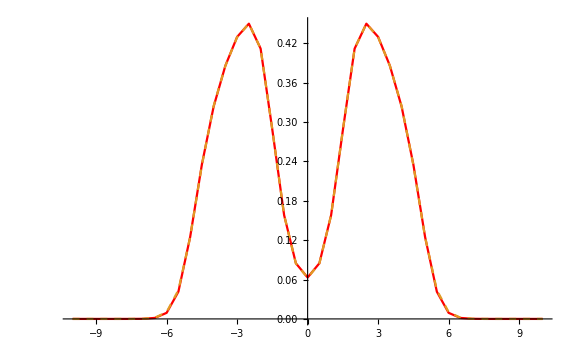

```mathematica
ListPlot[{TrueFunc1,GalerkGuess1},Joined->True,PlotStyle->{Red,Dashed},PlotRange->All]
```

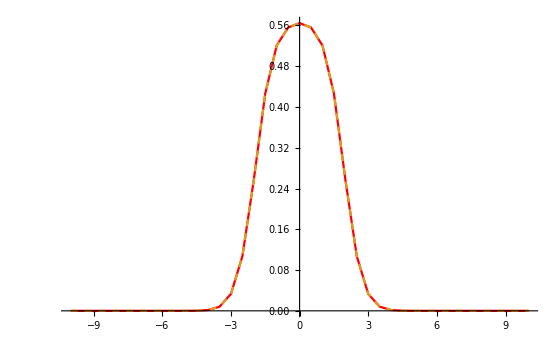

```mathematica
ListPlot[{TrueFunc2,GalerkGuess2},Joined->True,PlotStyle->{Red,Dashed},PlotRange->All]
```

```mathematica
CheaterFitter[testWF1_,testWF2_,targetWF1_,targetWF2_]:=Module[{chi2A,chi2B,coeffcheatA,coeffcheatB},
chi2A=0;
chi2B=0;

chi2A=chi2A+Sum[  (testWF1[[i]]-  targetWF1[[i]] )^2,{i,1,Length[testWF1]}];chi2B=chi2B+Sum[  (testWF2[[i]]-  targetWF2[[i]] )^2,{i,1,Length[testWF2]}];


coeffcheatA=FindMinimum[chi2A,Transpose[{listCoeff1,ConstantArray[0,numTrain]}]][[2]];
coeffcheatB=FindMinimum[chi2B,Transpose[{listCoeff2,ConstantArray[0,numTrain]}]][[2]];
Join[coeffcheatA,coeffcheatB]







]
```

```mathematica
LambdaEstimator[WF1_,WF2_,q_,k_]:=Module[{lam1Est,lam2Est},
lam1Est=(Dot[WF1,
Dot[-lap,WF1]+k*(x^2)*WF1+q*WF1*(WF1^2+WF2^2)])/Dot[WF1,WF1];
lam2Est=(Dot[WF2,
Dot[-lap,WF2]+(k+1)*(x^2)*WF2+q*WF2*(WF1^2+WF2^2)])/Dot[WF2,WF2];
{lam1Est,lam2Est}


]
```

```mathematica
MagicCoefficients=CheaterFitter[testPhi1,testPhi2,Flatten[phi1/.sol[qTest,K0]],Flatten[phi2/.sol[qTest,K0]]];
```

```mathematica
MagicFunc1=Transpose[{x,Flatten[testPhi1/.MagicCoefficients]/Sqrt[dx]}];
MagicFunc2=Transpose[{x,Flatten[testPhi2/.MagicCoefficients]/Sqrt[dx]}];
```

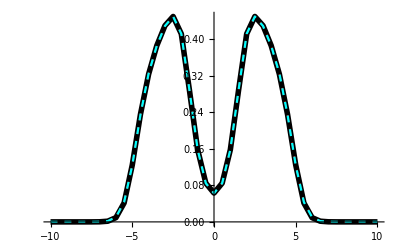

```mathematica
ListPlot[{TrueFunc1,GalerkGuess1,MagicFunc1},Joined->True,PlotStyle->{{Black,Thickness[0.01]},{Red,Dashed,Thickness[0.003]},{Cyan,Dashed,Thickness[0.004]},{Magenta,Dashed,Thickness[0.004]}},PlotRange->All]
```

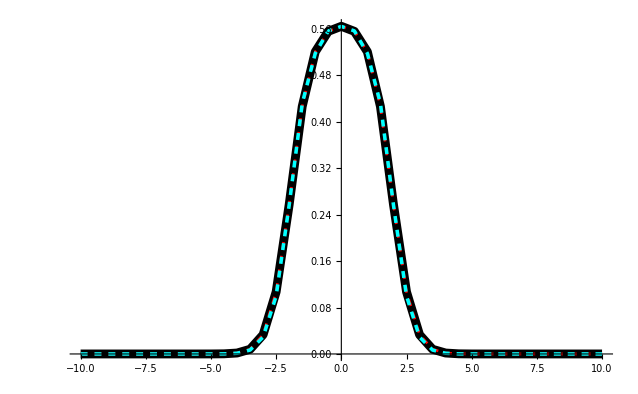

```mathematica
ListPlot[{TrueFunc2,GalerkGuess2,MagicFunc2},Joined->True,PlotStyle->{{Black,Thickness[0.01]},{Red,Dashed,Thickness[0.003]},{Cyan,Dashed,Thickness[0.004]}},PlotRange->All]
```

```mathematica
Residuals1Cheat=Table[{MagicFunc1[[i]][[1]],MagicFunc1[[i]][[2]]-TrueFunc1[[i]][[2]]},{i,1,Length[MagicFunc1]}];
Residuals2Cheat=Table[{MagicFunc2[[i]][[1]],MagicFunc2[[i]][[2]]-TrueFunc2[[i]][[2]]},{i,1,Length[MagicFunc2]}];
```

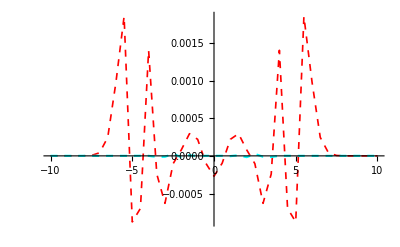

```mathematica
ListPlot[{Residuals1Cheat,Residuals2Cheat},Joined->True,PlotStyle->{{Red,Dashed,Thickness[0.003]},{Cyan,Dashed,Thickness[0.004]}},PlotRange->All]
```

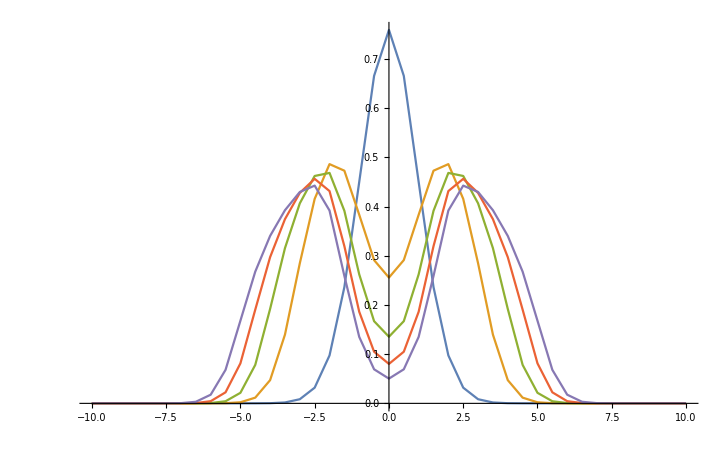

```mathematica
Show[ListPlot[Table[Transpose[{x,listPhi1[[kk]]/Sqrt[dx]}],{kk,1,Length[listPhi1]}],Joined->True,PlotRange->All]]
```

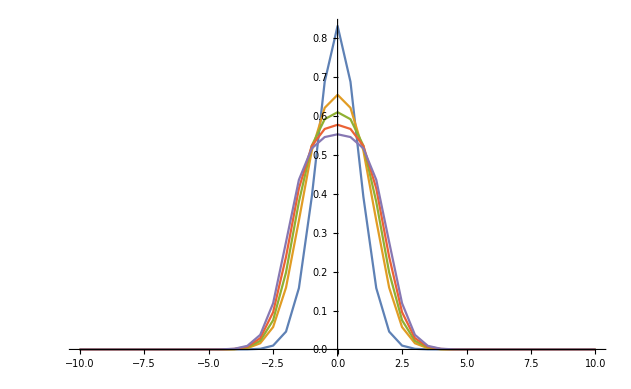

```mathematica
Show[ListPlot[Table[Transpose[{x,listPhi2[[kk]]/Sqrt[dx]}],{kk,1,Length[listPhi2]}],Joined->True,PlotRange->All]]
```

## Making some statistics

```mathematica
TrainingPoints={{0,0.5},{0,10},{50,0.5},{50,10}}(*{q,k}*)
```

{{0,0.5},{0,10},{50,0.5},{50,10}}

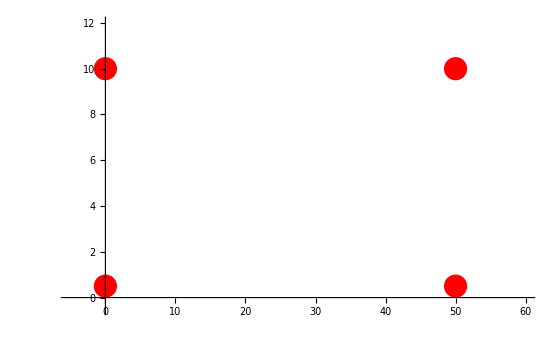

```mathematica
Show[ListPlot[TrainingPoints,PlotStyle->{PointSize[0.03],Red},PlotRange->{{-5,60},{-0.5,12}}]]
```

```mathematica
SeedMaker[q_,k_,trainingpoints_,lamvals1_,lamvals2_]:=Module[{ProximityFactors,lam1S,lam2S,NormS},
ProximityFactors=Table[ Exp[-(q-trainingpoints[[KK]][[1]])^2/(2*(25^2))-(k-trainingpoints[[KK]][[2]])^2]/(2*(5^2)) ,{KK,1,Length[trainingpoints]}];
NormS=Sum[ProximityFactors[[KK]],{KK,1,Length[trainingpoints]}];
lam1S=Sum[ProximityFactors[[KK]]*lamvals1[[KK]],{KK,1,Length[trainingpoints]}]/NormS;
lam2S=Sum[ProximityFactors[[KK]]*lamvals2[[KK]],{KK,1,Length[trainingpoints]}]/NormS;

Join[{lam1S,lam2S},ProximityFactors/NormS,ProximityFactors/NormS]


]
```

```mathematica
TestingPoints=Table[{i,j},{i,0,50,5},{j,0.5,10,1}];
```

```mathematica
Length[Flatten[TestingPoints,1]]
```

110

```mathematica
numTrain=Length[TrainingPoints]; (*Number of training points*)
```

```mathematica
listPhi1=Array[trainPhi1,{numTrain,len}]; (*List of the training functions 'phi'*)
listPhi2=Array[trainPhi2,{numTrain,len}];
listCoeff1=Array[aTest1,numTrain];
listCoeff2=Array[aTest2,numTrain];(*Coefficients of the Galerkin approximated solution*)
```

```mathematica
lambdasPhi1=ConstantArray[0,numTrain];
lambdasPhi2=ConstantArray[0,numTrain];
```

```mathematica
For[i=1,i<=numTrain,i++,
{listPhi1[[i]],listPhi2[[i]],lambdasPhi1[[i]],lambdasPhi2[[i]]}={phi1,phi2,lam1,lam2}/.sol[TrainingPoints[[i]][[1]],TrainingPoints[[i]][[2]]];
]
```

```mathematica
testPhi1=Dot[Transpose[listPhi1],listCoeff1];
testPhi2=Dot[Transpose[listPhi2],listCoeff2];
```

```mathematica
ResultsGarlekinSeedMaker={};
```

```mathematica
FailedParamsGarlekinSeedMaker={};
```

```mathematica
ResultsGarlekinSeedCheater={};
```

```mathematica
FailedParamsGarlekinSeedCheater={};
```

```mathematica
ResultsCheaterCoeffs={};
```

```mathematica
For[i=1,i≤Length[TestingPoints],i++,
Print[i];


For[j=1,j<=Length[TestingPoints[[i]]], j++,



FlagGarlekinSeedMaker=0;
FlagGarlekinSeedCheater=0;

(*Results made with a flat seed:*)
(*Check[solGaler=GalerkinSolverTrained[TestingPoints[[i]][[j]][[1]],TestingPoints[[i]][[j]][[2]],listPhi1,listPhi2,testPhi1,testPhi2,{1,1,0.1,0.1,0.1,0.1}],Flag=1];*)

SolPhi1=Flatten[phi1/.sol[TestingPoints[[i]][[j]][[1]],TestingPoints[[i]][[j]][[2]]]];
SolPhi2=Flatten[phi2/.sol[TestingPoints[[i]][[j]][[1]],TestingPoints[[i]][[j]][[2]]]];


(*Results made with an adjustable seed::*)
Check[solGalerSeedMaker=GalerkinSolverTrained[TestingPoints[[i]][[j]][[1]],TestingPoints[[i]][[j]][[2]],listPhi1,listPhi2,testPhi1,testPhi2,SeedMaker[TestingPoints[[i]][[j]][[1]],TestingPoints[[i]][[j]][[2]],TrainingPoints,lambdasPhi1,lambdasPhi2]],FlagGarlekinSeedMaker=1];



(*Results made with a cheat seed::*)
(*Check[solGalerSeedCheater=GalerkinSolverTrained[TestingPoints[[i]][[j]][[1]],TestingPoints[[i]][[j]][[2]],listPhi1,listPhi2,testPhi1,testPhi2,Join[SeedMaker[TestingPoints[[i]][[j]][[1]],TestingPoints[[i]][[j]][[2]],TrainingPoints,lambdasPhi1,lambdasPhi2][[1;;2]],
listCoeff/.CheaterFitter[testPhi1,testPhi2,SolPhi1,SolPhi2]


]],FlagGarlekinSeedCheater=1];*)

(*solGalerSeedCheater=GalerkinSolverTrained[TestingPoints[[i]][[j]][[1]],TestingPoints[[i]][[j]][[2]],listPhi1,listPhi2,testPhi1,testPhi2,Join[SeedMaker[TestingPoints[[i]][[j]][[1]],TestingPoints[[i]][[j]][[2]],TrainingPoints,lambdasPhi1,lambdasPhi2][[1;;2]],
listCoeff/.CheaterFitter[testPhi1,testPhi2,SolPhi1,SolPhi2]]];*)

solGalerSeedCheater=GalerkinSolverTrained[TestingPoints[[i]][[j]][[1]],TestingPoints[[i]][[j]][[2]],listPhi1,listPhi2,testPhi1,testPhi2,Join[LambdaEstimator[

Flatten[testPhi1/.CheaterFitter[testPhi1,testPhi2,SolPhi1,SolPhi2]],

Flatten[testPhi2/.CheaterFitter[testPhi1,testPhi2,SolPhi1,SolPhi2]],


TestingPoints[[i]][[j]][[1]],TestingPoints[[i]][[j]][[2]]],
Flatten[{listCoeff1,listCoeff1}/.CheaterFitter[testPhi1,testPhi2,SolPhi1,SolPhi2]]]];


If[FlagGarlekinSeedMaker==0,
AppendTo[ResultsGarlekinSeedMaker,{TestingPoints[[i]][[j]],solGalerSeedMaker}],
AppendTo[FailedParamsGarlekinSeedMaker,{TestingPoints[[i]][[j]][[1]],TestingPoints[[i]][[j]][[2]]}]];

(*If[FlagGarlekinSeedCheater==0,
AppendTo[ResultsGarlekinSeedCheater,{TestingPoints[[i]][[j]],solGalerSeedCheater}],
AppendTo[FailedParamsGarlekinSeedCheater,{TestingPoints[[i]][[j]][[1]],TestingPoints[[i]][[j]][[2]]}]];*)

AppendTo[ResultsGarlekinSeedCheater,{TestingPoints[[i]][[j]],solGalerSeedCheater}];



AppendTo[ResultsCheaterCoeffs,{TestingPoints[[i]][[j]],LambdaEstimator[

Flatten[testPhi1/.CheaterFitter[testPhi1,testPhi2,SolPhi1,SolPhi2]],

Flatten[testPhi2/.CheaterFitter[testPhi1,testPhi2,SolPhi1,SolPhi2]],


TestingPoints[[i]][[j]][[1]],TestingPoints[[i]][[j]][[2]]]}];








];





]
```

1

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

2

3

4

5

6

7

8

9

10

11

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
ResultsEnergy1SeedMaker={};
ResultsEnergy2SeedMaker={};
ResultsEnergy1SeedCheater={};
ResultsEnergy2SeedCheater={};
```

```mathematica
ResultsEnergy1CheatCoeffs={};
ResultsEnergy2CheatCoeffs={};
```

```mathematica
For[i=1,i≤Length[ResultsGarlekinSeedCheater],i++,


AppendTo[ResultsEnergy1SeedCheater, ((lam21/.ResultsGarlekinSeedCheater[[i]][[2]])- lam1/.sol[ResultsGarlekinSeedCheater[[i]][[1]][[1]],ResultsGarlekinSeedCheater[[i]][[1]][[2]]])/( lam1/.sol[ResultsGarlekinSeedCheater[[i]][[1]][[1]],ResultsGarlekinSeedCheater[[i]][[1]][[2]]]) ];

AppendTo[ResultsEnergy2SeedCheater, ((lam22/.ResultsGarlekinSeedCheater[[i]][[2]])- lam2/.sol[ResultsGarlekinSeedCheater[[i]][[1]][[1]],ResultsGarlekinSeedCheater[[i]][[1]][[2]]])/( lam2/.sol[ResultsGarlekinSeedCheater[[i]][[1]][[1]],ResultsGarlekinSeedCheater[[i]][[1]][[2]]]) ];


]
```

```mathematica
For[i=1,i≤Length[ResultsGarlekinSeedMaker],i++,


AppendTo[ResultsEnergy1SeedMaker, ((lam21/.ResultsGarlekinSeedMaker[[i]][[2]])- lam1/.sol[ResultsGarlekinSeedMaker[[i]][[1]][[1]],ResultsGarlekinSeedMaker[[i]][[1]][[2]]])/( lam1/.sol[ResultsGarlekinSeedMaker[[i]][[1]][[1]],ResultsGarlekinSeedMaker[[i]][[1]][[2]]]) ];

AppendTo[ResultsEnergy2SeedMaker, ((lam22/.ResultsGarlekinSeedMaker[[i]][[2]])- lam2/.sol[ResultsGarlekinSeedMaker[[i]][[1]][[1]],ResultsGarlekinSeedMaker[[i]][[1]][[2]]])/( lam2/.sol[ResultsGarlekinSeedMaker[[i]][[1]][[1]],ResultsGarlekinSeedMaker[[i]][[1]][[2]]]) ];


]
```

```mathematica
For[i=1,i≤Length[ResultsCheaterCoeffs],i++,


AppendTo[ResultsEnergy1CheatCoeffs, (ResultsCheaterCoeffs[[i]][[2]][[1]]- lam1/.sol[ResultsCheaterCoeffs[[i]][[1]][[1]],ResultsCheaterCoeffs[[i]][[1]][[2]]])/( lam1/.sol[ResultsCheaterCoeffs[[i]][[1]][[1]],ResultsCheaterCoeffs[[i]][[1]][[2]]]) ];

AppendTo[ResultsEnergy2CheatCoeffs, (ResultsCheaterCoeffs[[i]][[2]][[2]]- lam2/.sol[ResultsCheaterCoeffs[[i]][[1]][[1]],ResultsCheaterCoeffs[[i]][[1]][[2]]])/( lam2/.sol[ResultsCheaterCoeffs[[i]][[1]][[1]],ResultsCheaterCoeffs[[i]][[1]][[2]]]) ];


]
```

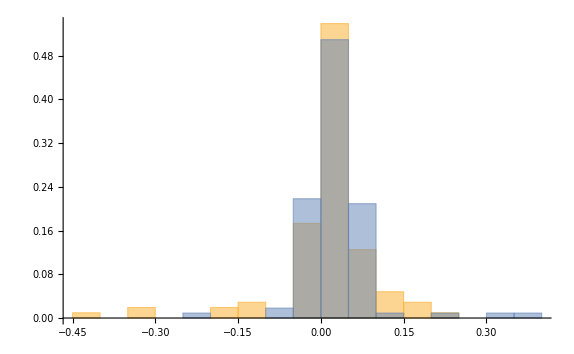

```mathematica
Histogram[{ResultsEnergy1SeedMaker,ResultsEnergy1SeedCheater},20,"Probability"]
```

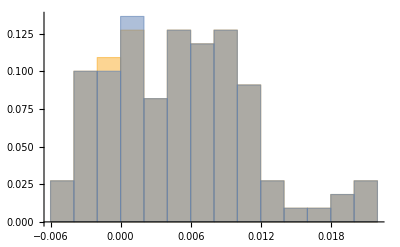

```mathematica
Histogram[{ResultsEnergy1SeedMaker,ResultsEnergy1SeedCheater},10,"Probability"]
```

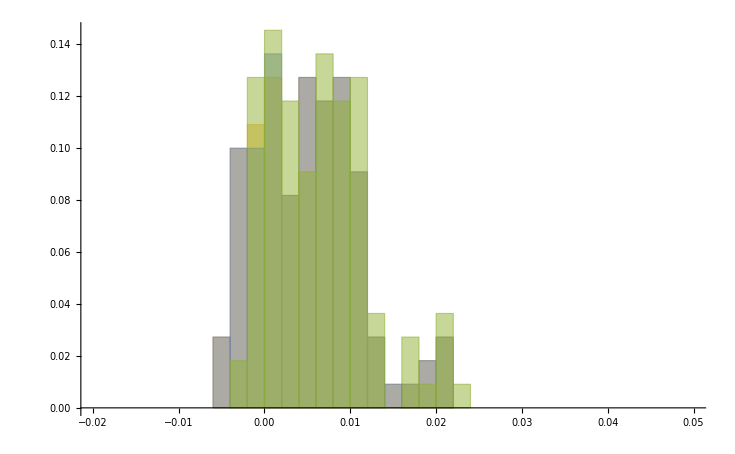

```mathematica
Histogram[{ResultsEnergy1SeedMaker,ResultsEnergy1SeedCheater,ResultsEnergy1CheatCoeffs},10,"Probability",PlotRange->{{-0.02,0.05},All}]
```